## neutral logistics

```mathematica
Quit[]
```

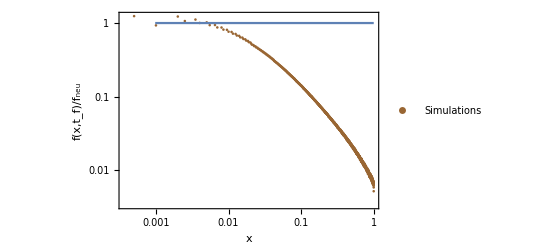

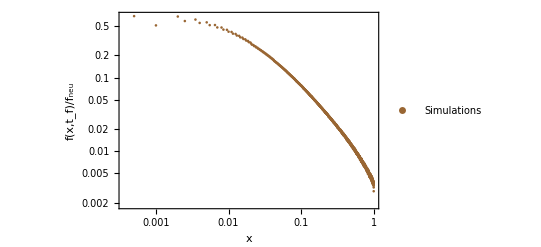

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
f=0.818;
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_t_100_recombination_0.01_more_loci.txt"];

datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,(1+f)x11s x21s/theta};

a1s=ListLogLogPlot[{Data1s}, Frame->True,FrameLabel->{"x","f(x,t_f)/f_neu"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Brown},PlotLegends->{"Simulations", "Diffusion"}];
a2s=LogLogPlot[1,{x,0,1}];

Show[a1s,a2s]
```

```mathematica
average frequency in neutral logistic is taken from below place
/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100
```

```mathematica
N1=1000;
mu=10^-7;
L=1000000;

theta=4 N1 mu L;(*theta=4 N mu*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_t_100_recombination_0.01_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

(*Filter out points where x21s is zero and x11s is 0 or 1*)
filteredData=Select[Transpose[{x11s,x21s}],#[[2]]!=0&&0<#[[1]]<1&];

x11sFiltered=filteredData[[All,1]];
x21sFiltered=filteredData[[All,2]];

Data1s=Transpose@{x11sFiltered,x11sFiltered x21sFiltered/theta};

(*Generate 100 logarithmically spaced indices within the filtered range*)
logIndices=Round[Exp[Range[Log[1],Log[Length[x11sFiltered]],(Log[Length[x11sFiltered]]-Log[1])/79]]];

(*Select the corresponding points*)
selectedData=Data1s[[logIndices]];

(*Plot the selected points*)
a1s=ListLogLogPlot[selectedData,Frame->True,FrameLabel->{"x","f(x,\!\(\*SubscriptBox[\(t\), \(f\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{" r = 0.01"},PlotMarkers->{"■",10}];
a1s=ListLogLogPlot[selectedData,Frame->True,FrameLabel->{"x","f(x,\!\(\*SubscriptBox[\(t\), \(f\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{" r = 0.01 "},PlotMarkers->{"■",10}];

Show[a1s]
```

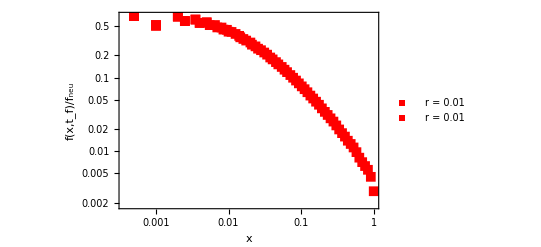

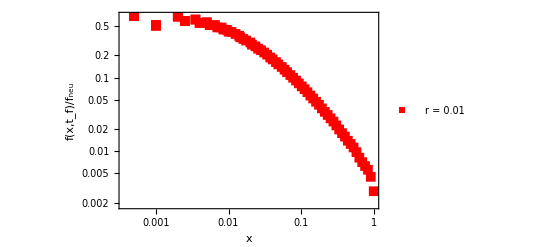

```mathematica
r01=-Graphics-;
```

```mathematica
Quit[]
```

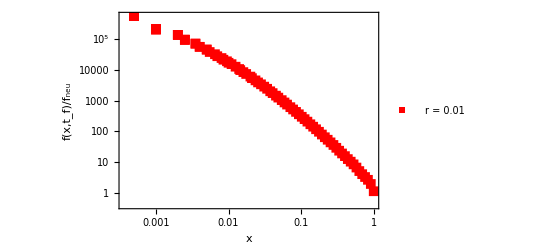

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
theta=4 N1 mu L;(*theta=4 N mu*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_t_100_recombination_0.01_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

(*Filter out points where x21s is zero and x11s is 0 or 1*)
filteredData=Select[Transpose[{x11s,x21s}],#[[2]]!=0&&0<#[[1]]<1&];

x11sFiltered=filteredData[[All,1]];
x21sFiltered=filteredData[[All,2]];

Data1s=Transpose@{x11sFiltered,x21sFiltered};

(*Generate 100 logarithmically spaced indices within the filtered range*)
logIndices=Round[Exp[Range[Log[1],Log[Length[x11sFiltered]],(Log[Length[x11sFiltered]]-Log[1])/79]]];

(*Select the corresponding points*)
selectedData=Data1s[[logIndices]];

ListLogLogPlot[selectedData,Frame->True,FrameLabel->{"x","f(x,\!\(\*SubscriptBox[\(t\), \(f\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Red},PlotLegends->{" r = 0.01 "},PlotMarkers->{"■",10}]

(*Show[a1s]*)
```

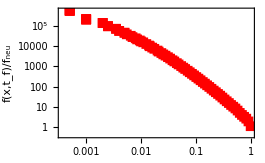
```mathematica
k1=-Graphics-;
```

```mathematica
Quit[]
```

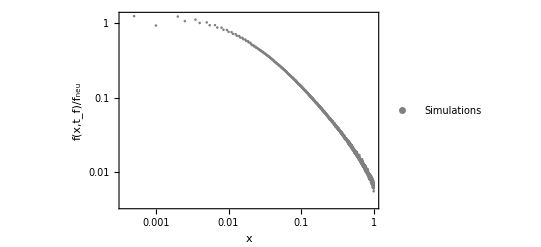

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
f=0.818;
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_t_100_recombination_0_more_loci.txt"];

datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,(1+f)x11s x21s/theta};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_f)/f_neu"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray},PlotLegends->{"Simulations", "Diffusion"}];
a2s=LogLogPlot[theta/x,{x,0,1}];

Show[a1s,a2s]
```

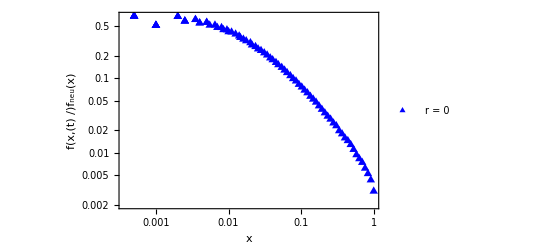

```mathematica
N1=1000;
mu=10^-7;
L=1000000;

theta=4 N1 mu L;(*theta=4 N mu*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_t_100_recombination_0_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

(*Filter out points where x21s is zero and x11s is 0 or 1*)
filteredData=Select[Transpose[{x11s,x21s}],#[[2]]!=0&&0<#[[1]]<1&];

x11sFiltered=filteredData[[All,1]];
x21sFiltered=filteredData[[All,2]];

Data1s=Transpose@{x11sFiltered,x11sFiltered x21sFiltered/theta};

(*Generate 100 logarithmically spaced indices within the filtered range*)
logIndices=Round[Exp[Range[Log[1],Log[Length[x11sFiltered]],(Log[Length[x11sFiltered]]-Log[1])/79]]];

(*Select the corresponding points*)
selectedData=Data1s[[logIndices]];

(*Plot the selected points*)
a1s=ListLogLogPlot[selectedData,Frame->True,FrameLabel->{"x","f(x,\!\(\*SubscriptBox[\(t\), \(f\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{" r = 0 "},PlotMarkers->{"▲",10}];
a1s=ListLogLogPlot[selectedData,Frame->True,FrameLabel->{Style["x",Italic,FontSize->16],Style["f(x,\!\(\*SubscriptBox[\(t\), \(fix\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)",Italic,FontSize->16]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Blue},PlotLegends->{" r = 0 "},PlotMarkers->{"▲",10}];
a1s=ListLogLogPlot[selectedData,Frame->True,FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t) /",Italic],Style["",Italic],""]//DisplayForm,Style["",Italic],SubscriptBox[Style["f",Italic],"StyleBox[\"neu\",FontSlant->\"Italic\"]"]//DisplayForm,Style["(x)",Italic]}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{" r = 0 "},PlotMarkers->{"▲",10}];

Show[a1s]
```

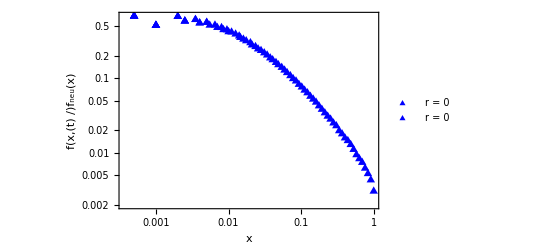

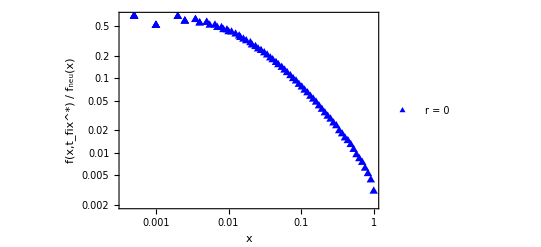

FrameLabel→{x,f(x,t_fix^*) / f_neu(x)}

```mathematica
r0=-Graphics-;
```

```mathematica
Diffusion as well
```

```mathematica
Quit[]
```

```mathematica
/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100
```

```mathematica
N1 = 1000;
sig=0.0;
f=sig/(2-sig);
N1= 1000/(1+f);
mu=10^-6;
L=10000;

theta=4 N1 mu L;

s=0.1;
h=0.5;
sa=s (h+ (1-h) f);
sb= s (1- (1-f) h);
x0=1/(2 2 sa N1);
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_frequency.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];
datap=Transpose@{x11s,x21s};
x1=Interpolation@datap;

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,100},{x,0,1}];
gData=Table[ G[x,100]/(x*(1-x)),{x,0.001,0.999,0.001}];

averageGData={};
AppendTo[averageGData,gData];
```

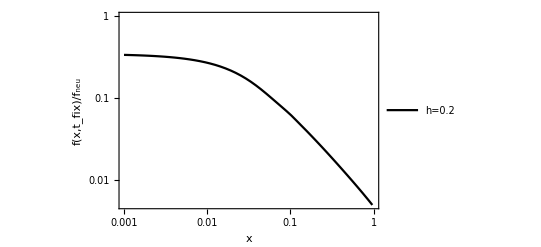

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.0;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,xaxis gData/theta};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red];


Data1s=Data;

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.5"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"■",12}];

a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Black},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.005,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
N1 = 1000;
sig=0.0;
f=sig/(2-sig);
N1= 1000/(1+f);
mu=10^-6;
L=10000;

theta=4 N1 mu L;

s=0.1;
h=0.5;
sa=s (h+ (1-h) f);
sb= s (1- (1-f) h);
x0=1/(2 2 sa N1);
x1=NDSolveValue[{D[x2a[t],t]==x2a[t]*(1-x2a[t]) (sa (1-x2a[t]) + sb x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[ G[x,100]/(x*(1-x)),{x,0.001,0.999,0.001}];

averageGData={};
AppendTo[averageGData,gData];
```

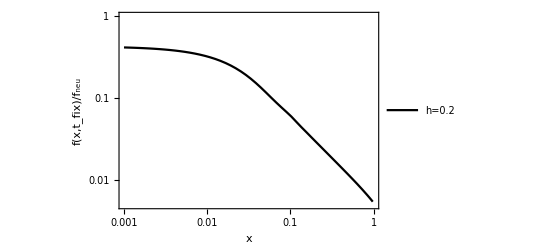

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.0;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,xaxis gData/theta};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red];


Data1s=Data;

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.5"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"■",12}];

a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Black},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.005,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```

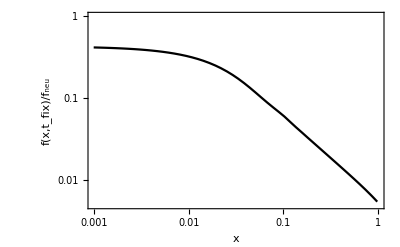
```mathematica
a2=-Graphics-;
```

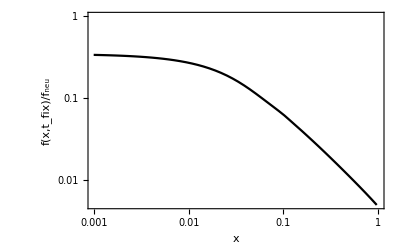
```mathematica
a1=-Graphics-;
```

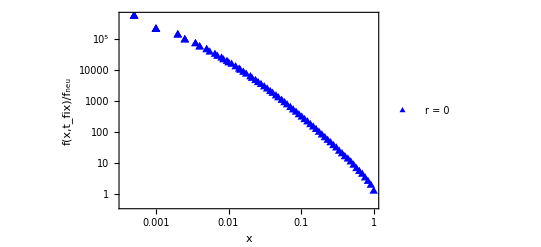

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
theta=4 N1 mu L;(*theta=4 N mu*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_t_100_recombination_0_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

(*Filter out points where x21s is zero and x11s is 0 or 1*)
filteredData=Select[Transpose[{x11s,x21s}],#[[2]]!=0&&0<#[[1]]<1&];

x11sFiltered=filteredData[[All,1]];
x21sFiltered=filteredData[[All,2]];

Data1s=Transpose@{x11sFiltered, x21sFiltered};

(*Generate 100 logarithmically spaced indices within the filtered range*)
logIndices=Round[Exp[Range[Log[1],Log[Length[x11sFiltered]],(Log[Length[x11sFiltered]]-Log[1])/79]]];

(*Select the corresponding points*)
selectedData=Data1s[[logIndices]];

(*Plot the selected points*)
a1s=ListLogLogPlot[selectedData,Frame->True,FrameLabel->{Style["x",Italic,FontSize->16],Style["f(x,\!\(\*SubscriptBox[\(t\), \(fix\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)",Italic,FontSize->16]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Blue},PlotLegends->{" r = 0 "},PlotMarkers->{"▲",10}];

Show[a1s]
```

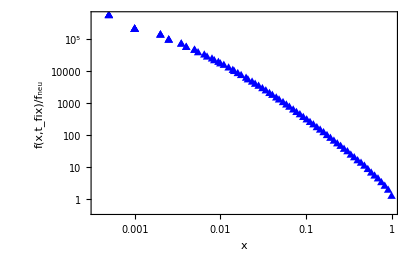
```mathematica
k2=-Graphics-;
```

```mathematica
Show[k2,k1]
```

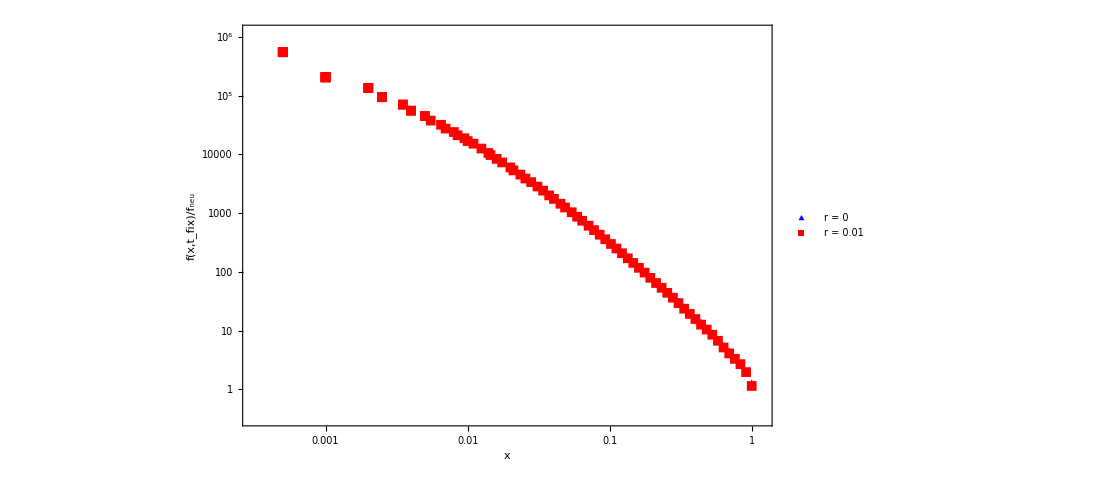

```mathematica
a3=-Graphics-;
```

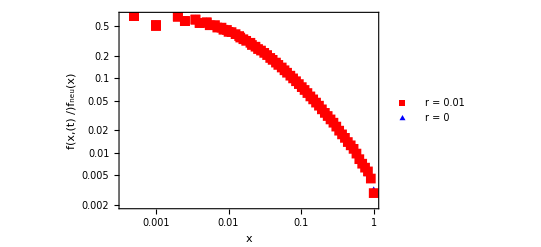

```mathematica
Show[a1s,r01]
```

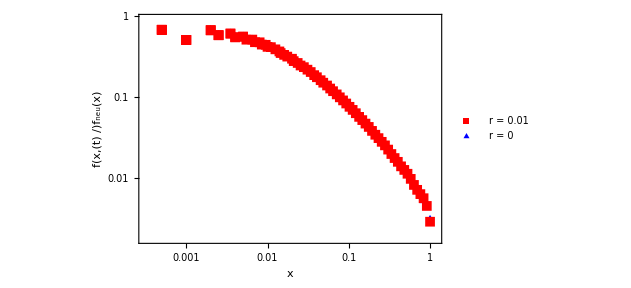
```mathematica
a2=-Graphics-;
```

```mathematica
a1=-Graphics-;
```

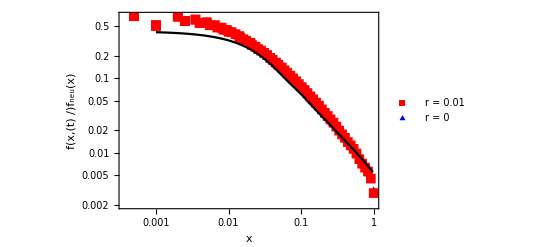

```mathematica
Show[a1s,r01,a1]
```

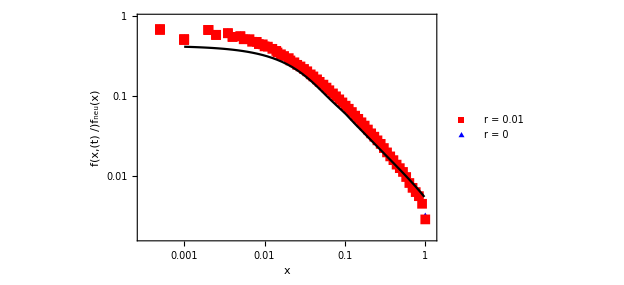

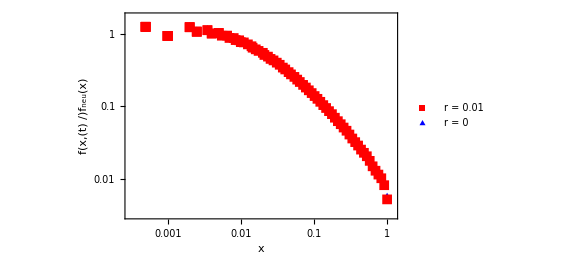

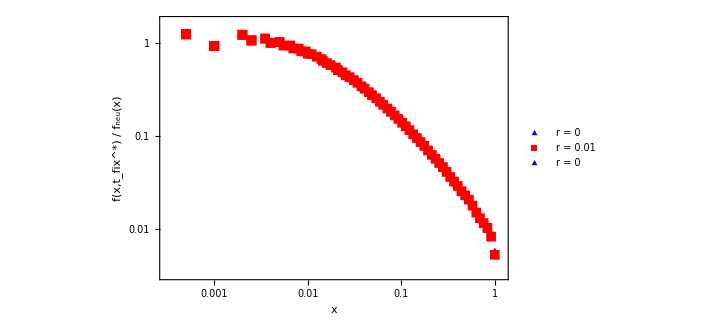

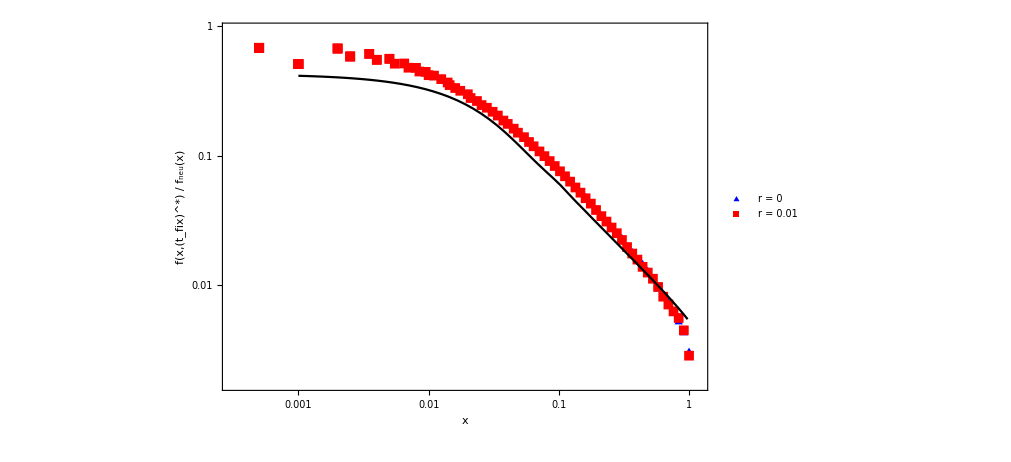

```mathematica
Show[a1,a3]
```

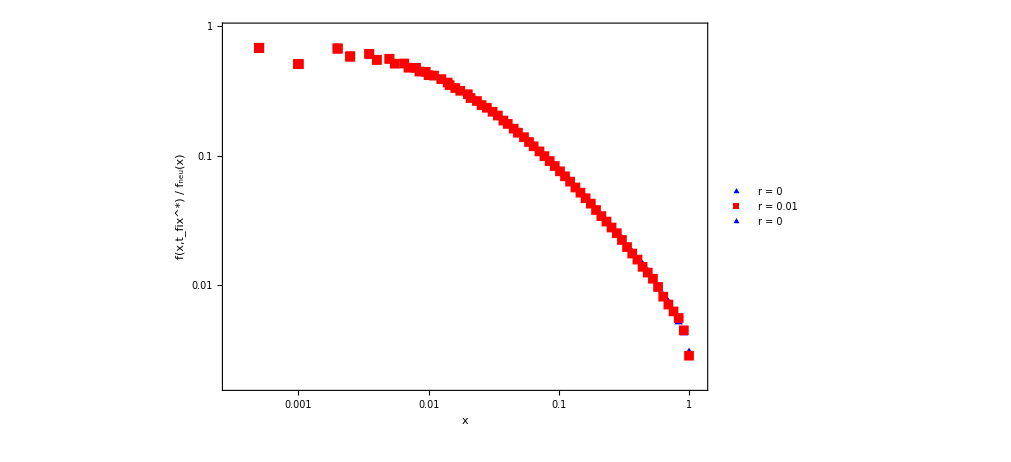
```mathematica
a1=-Graphics-;
```

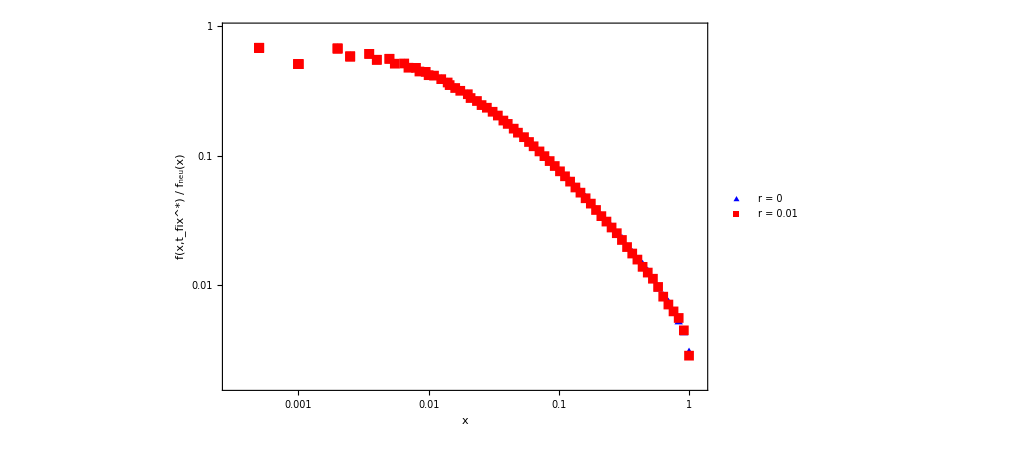

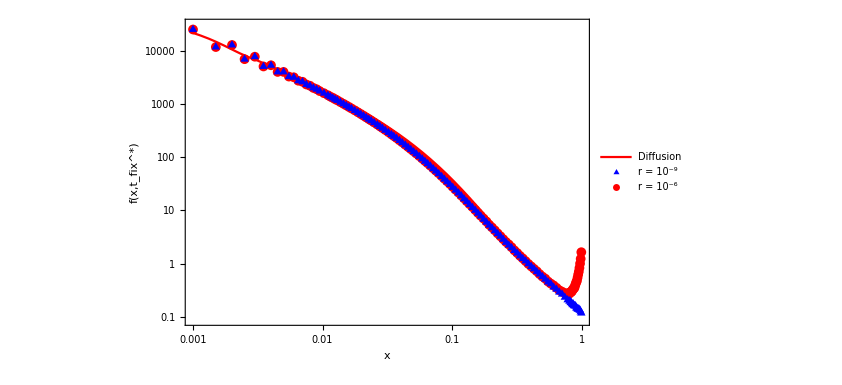

```mathematica
Show[a2,a1]
```

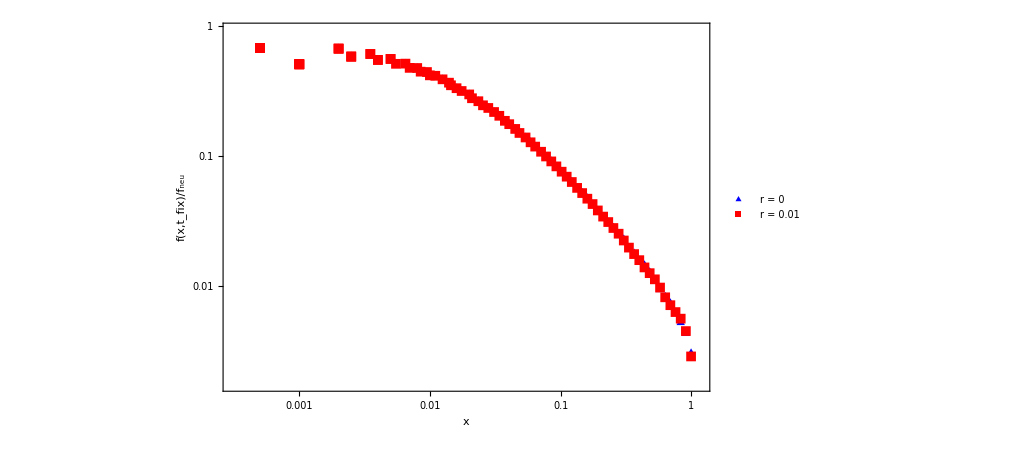

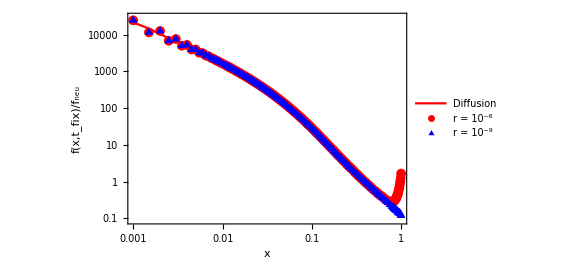

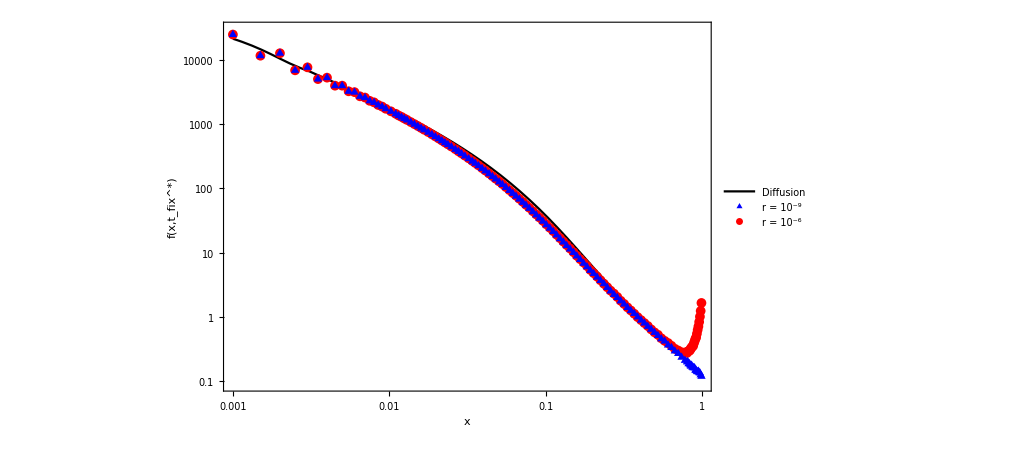

```mathematica
Show[a1,a2]
```

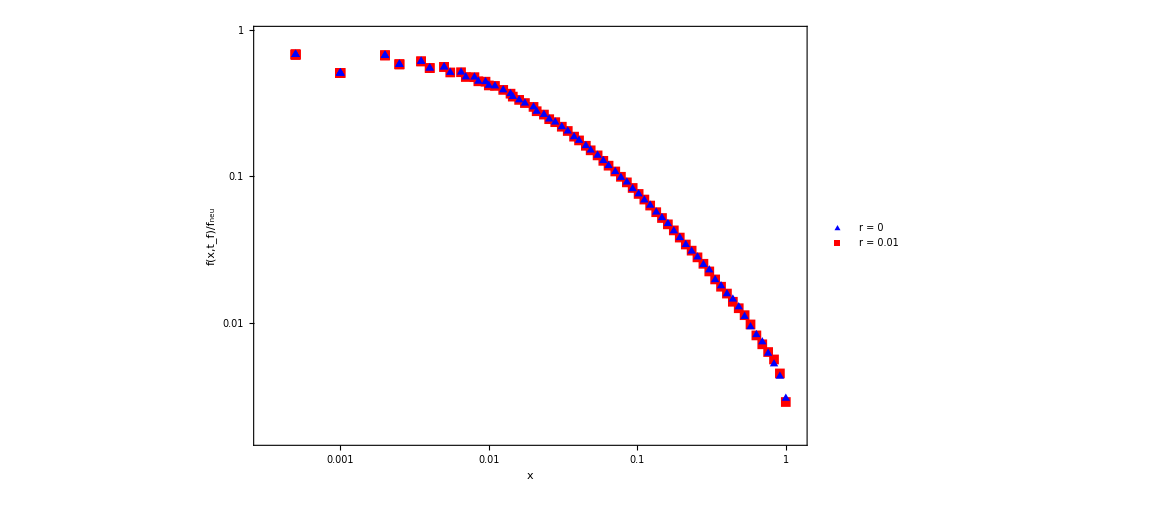

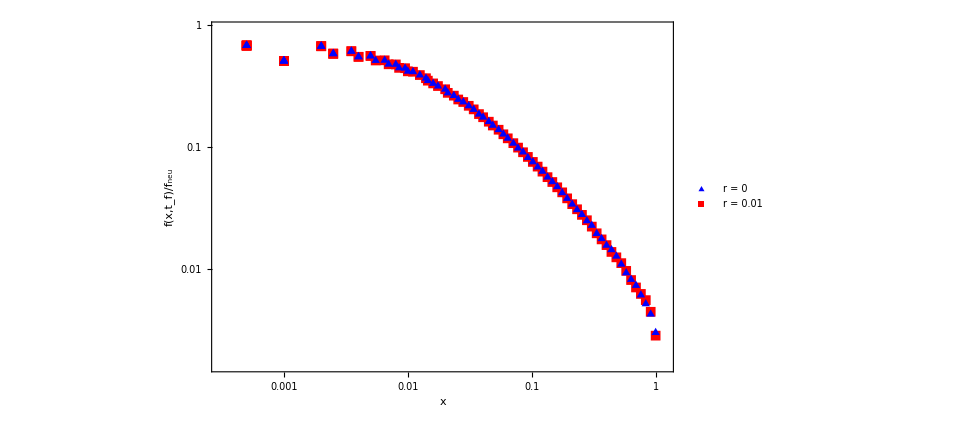

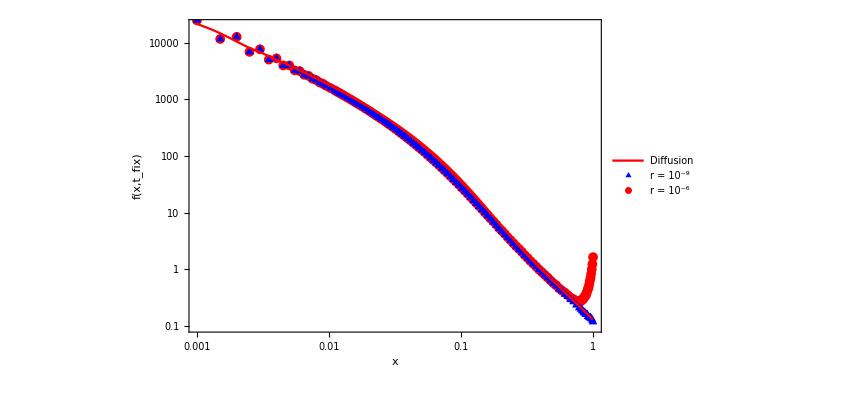

```mathematica
1000  10^-7  1000000
```

100

```mathematica
0.01 1000000
```

10000.

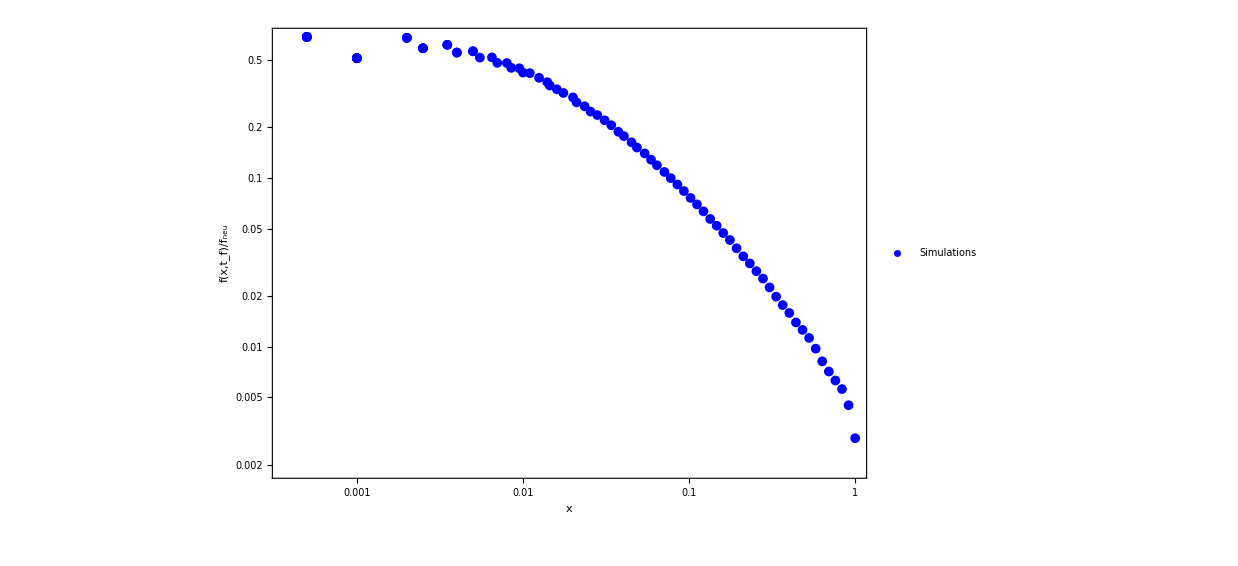

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
theta=4 N1 mu L;(*theta=4 N mu*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_t_100_recombination_0.01_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

(*Filter out points where x21s is zero and x11s is 0 or 1*)
filteredData=Select[Transpose[{x11s,x21s}],#[[2]]!=0&&0<#[[1]]<1&];

x11sFiltered=filteredData[[All,1]];
x21sFiltered=filteredData[[All,2]];

Data1s=Transpose@{x11sFiltered,x11sFiltered x21sFiltered/theta};

(*Generate 100 logarithmically spaced indices within the filtered range*)
logIndices=Round[Exp[Range[Log[1],Log[Length[x11sFiltered]],(Log[Length[x11sFiltered]]-Log[1])/79]]];

(*Select the corresponding points*)
selectedData=Data1s[[logIndices]];

(*Plot the selected points*)
a1s=ListLogLogPlot[selectedData,Frame->True,FrameLabel->{"x","f(x,\!\(\*SubscriptBox[\(t\), \(f\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Simulations"},PlotMarkers->{"●",10}];

Show[a1s]
```

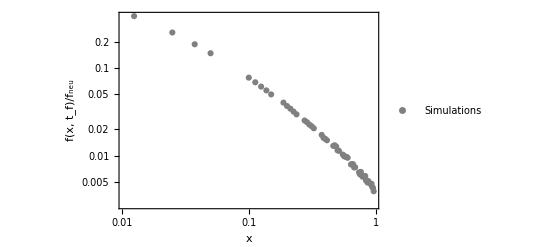

```mathematica
reducedData=Table[{x11s[[i]],x11s[[i]] x21s[[i]]/theta},{i,1,Length[x11s],25}];
a1s=ListLogLogPlot[reducedData,Frame->True,FrameLabel->{"x","f(x, \!\(\*SubscriptBox[\(t\), \(f\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray},PlotLegends->{"Simulations"}]
```

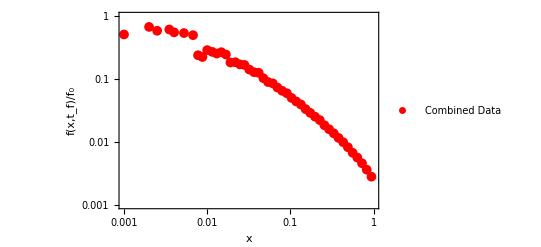

```mathematica
(*Define parameters*)N1=1000;
mu=10^-7;
L=1000000;
theta=4 N1 mu L;(*theta=2 N mu*)(*Read data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_t_100_recombination_0_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

(*Extract data*)
x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

(*Create Data1s*)
Data1s=Transpose[{x11s,x11s x21s/theta}];

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=50;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=xThreshold) and smoothed part (x>xThreshold)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,\!\(\*SubscriptBox[\(t\), \(f\)]\))/\!\(\*SubscriptBox[\(f\), \(0\)]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,1}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,\!\(\*SubscriptBox[\(t\), \(f\)]\))/\!\(\*SubscriptBox[\(f\), \(0\)]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"Combined Data"},PlotRange->{{0.001,1},{0.001,1}},PlotMarkers->{"●",10}];

(*Show both plots*)
Show[a1sCombined]
```

## FULL POPULATION RECOMBINATION inset

```mathematica
Quit[]
```

InputStream[…]

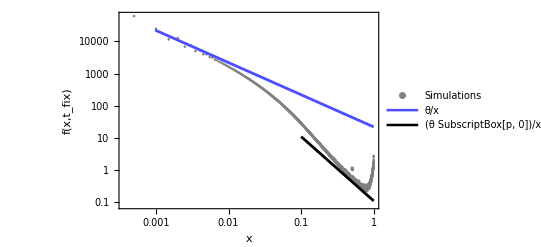

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.8181818181818181;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/Inbreeeding_recombination/average_data_s_9_r_6.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray,Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"}];


a2s=LogLogPlot[theta/(x),{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta/(2 1000 2 0.5 0.1 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s,a3s]
```

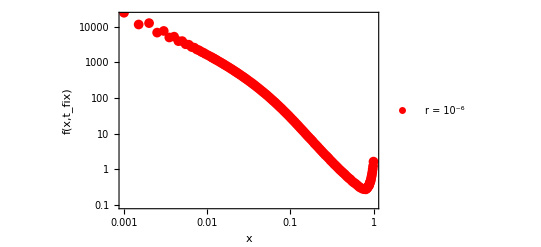

```mathematica
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/Inbreeeding_recombination/average_data_s_9_r_6.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

(*Data1s=Transpose@{x11s,x11s x21s/theta};*)
Data1s=Transpose@{x11s, x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xMin_,xMax_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x is between xMin and xMax*)filteredData=Select[data,xMin<#[[1]]<xMax&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xMinThreshold=0.005;(*Lower threshold for binning*)xMaxThreshold=0.8;(*Upper threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xMinThreshold,xMaxThreshold];

(*Define a separate binning function for the upper part with 1000 bins*)
smoothUpperData[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>=xThreshold*)filteredData=Select[data,#[[1]]>=xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to the upper part of the data*)
numBinsUpper=20;(*Number of bins for the upper part*)upperSmoothedData=smoothUpperData[Data1s,numBinsUpper,xMaxThreshold];

(*Separate data into three parts:lower part (x<=xMinThreshold),middle part (xMinThreshold<x<xMaxThreshold),and upper part (x>=xMaxThreshold)*)
lowerPart=Select[Data1s,#[[1]]<=xMinThreshold&];
middlePart=Select[smoothedData,xMinThreshold<#[[1]]<xMaxThreshold&];
upperPart=Select[upperSmoothedData,#[[1]]>=xMaxThreshold&];

(*Combine all parts*)
combinedData=Join[lowerPart,middlePart,upperPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,\!\(\*SubscriptBox[\(t\), \(fix\)]\))"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Red},PlotLegends->{" r = 10^-6 "},PlotRange->{{0.001,1},{0.1,20000}},PlotMarkers->{"●",10}];

(*Show both plots*)
Show[a1sCombined]
```

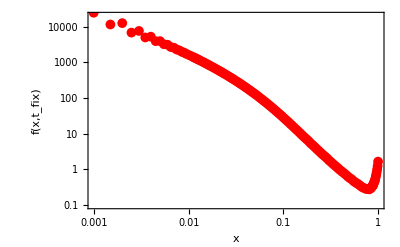
```mathematica
r6=-Graphics-;
```

```mathematica
Quit[]
```

InputStream[…]

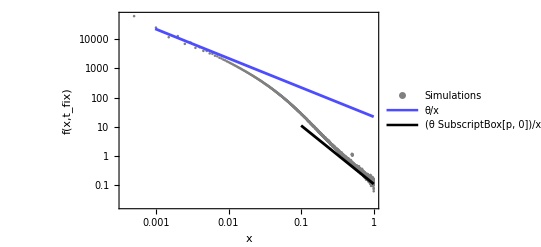

```mathematica
N1=1000;
mu=10^-6;
L=10000;
f=0.8181818181818181;
sa=(h + (1-h) f);
N1=N1/(1+f);
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/Inbreeeding_recombination/average_data_s_9_r_9.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray,Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"}];


a2s=LogLogPlot[theta/(x),{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta/(2 1000 2 0.5 0.1 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s,a3s]
```

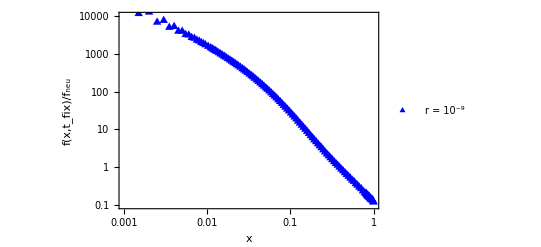

```mathematica
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/Inbreeeding_recombination/average_data_s_9_r_9.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

(*Data1s=Transpose@{x11s,x11s x21s/theta};*)
Data1s=Transpose@{x11s, x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xMin_,xMax_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x is between xMin and xMax*)filteredData=Select[data,xMin<#[[1]]<xMax&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xMinThreshold=0.005;(*Lower threshold for binning*)xMaxThreshold=0.8;(*Upper threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xMinThreshold,xMaxThreshold];

(*Define a separate binning function for the upper part with 1000 bins*)
smoothUpperData[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>=xThreshold*)filteredData=Select[data,#[[1]]>=xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to the upper part of the data*)
numBinsUpper=20;(*Number of bins for the upper part*)upperSmoothedData=smoothUpperData[Data1s,numBinsUpper,xMaxThreshold];

(*Separate data into three parts:lower part (x<=xMinThreshold),middle part (xMinThreshold<x<xMaxThreshold),and upper part (x>=xMaxThreshold)*)
lowerPart=Select[Data1s,#[[1]]<=xMinThreshold&];
middlePart=Select[smoothedData,xMinThreshold<#[[1]]<xMaxThreshold&];
upperPart=Select[upperSmoothedData,#[[1]]>=xMaxThreshold&];

(*Combine all parts*)
combinedData=Join[lowerPart,middlePart,upperPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,\!\(\*SubscriptBox[\(t\), \(fix\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Blue},PlotLegends->{" r = 10^-9 "},PlotRange->{{0.001,1},{0.1,10000}},PlotMarkers->{"▲",10}];

(*Show both plots*)
Show[a1sCombined]
```

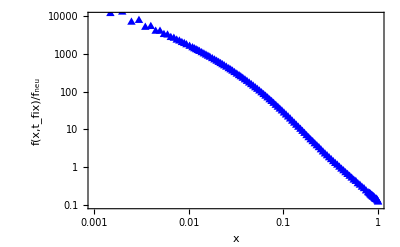
```mathematica
r9=-Graphics-;
```

```mathematica
Show[a3,a1,a2]
```

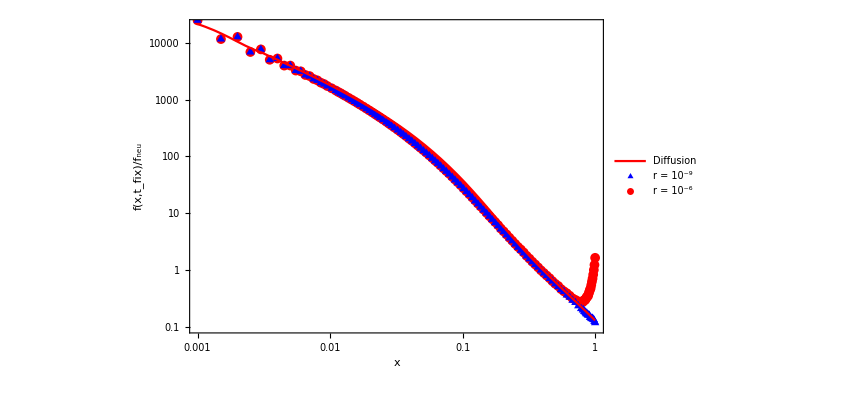

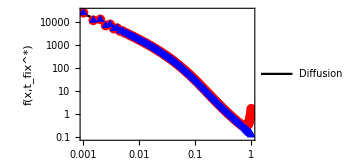

```mathematica
Show[a1sInterpolated,r6,r9]
```

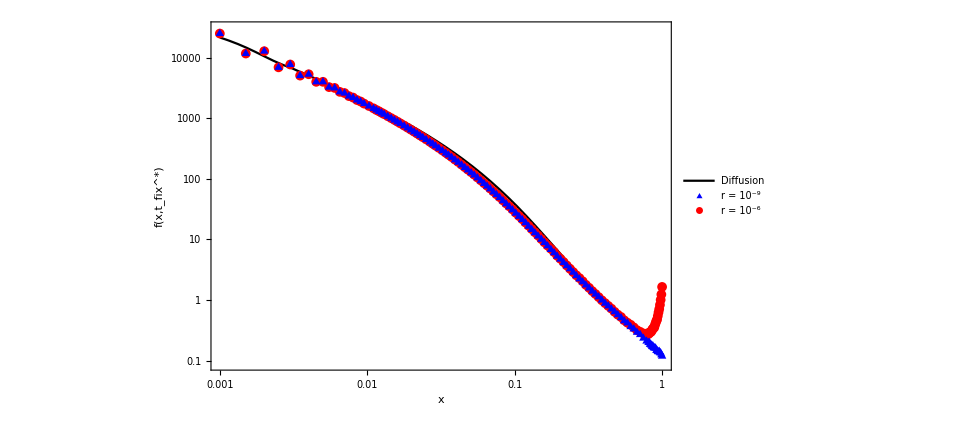

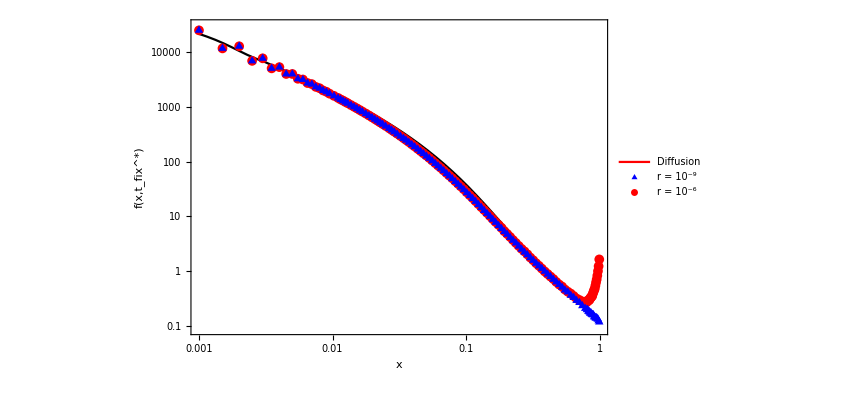

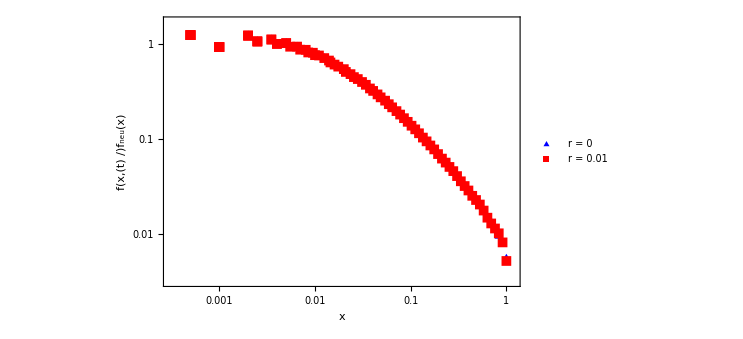

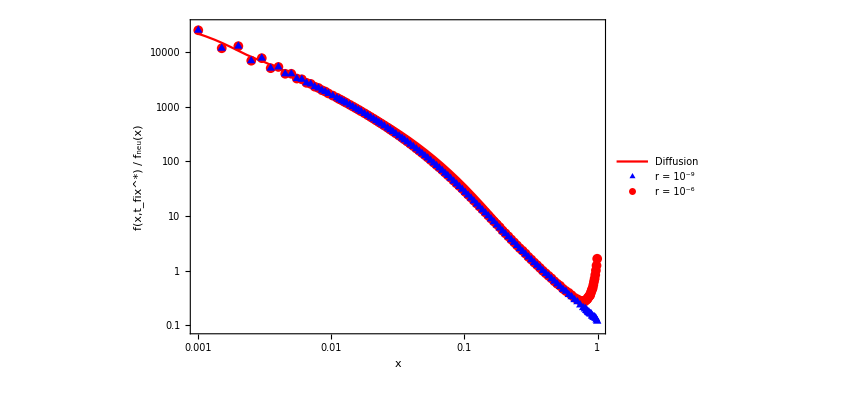

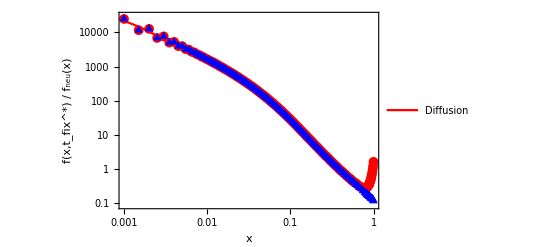

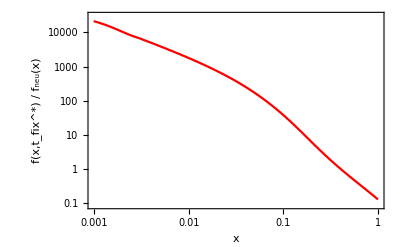
```mathematica
diff=-Graphics-;
```

```mathematica
Quit[]
```

```mathematica
N1 = 1000;

sbar = 0.1 ;
x0 = 1/(2 N1);
h=0.5;
s[t_] :=(sbar);
sig=0.9;
F=sig/(2-sig);
N1=N1/(1+F);
sa=(h + (1-h) F);
sb=(1-(1-F) h);
k=1;
taui[t_] :=sa∫_0^t s[t1]ⅆt1;
pf1= ( 2/( NIntegrate[(E^(-taui[t])),{t,0,Infinity}]));
A= (sa-sb)/sb Log[sa/sb];
c1=pf1/(1-pf1);
ck=(1-(1-pf1)^k)/(1-pf1)^k;
C1=2 N1 pf1 ⅇ^-A ;
B[Te_]:= (2 N1)/NIntegrate[ⅇ^(sb/sa  taui[t]),{t,0,Te}];
Pnew[Te_]:=(sa 1 c1)/(sb ck)  (C1  B[Te]^2)/(2 N1) ⅇ^(sb/sa taui[Te]) NIntegrate[q^(-sa/sb) ⅇ^(-B[Te] q) ⅇ^(-C1 q^(-sa/sb))  Hypergeometric1F1[1-k,2,-C1 c1 q^(-sa/sb)],{q,0,Infinity},MaxRecursion->20];
NIntegrate[Te Pnew[Te],{Te,10,500},PrecisionGoal->15,WorkingPrecision->30,MaxRecursion->15]
```

NIntegrate::nlim: t = Te is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand (1. ⅇ^(-200./q^1.-(1100. q)/NIntegrate[«1»]))/q^1. has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::precw: The precision of the argument function ((220000. ⅇ^(0.0909091 Te) Te NIntegrate[«1»])/(NIntegrate[ⅇ^((«19» «1»)/(«19»)),{t,0,Te}]^2)) is less than WorkingPrecision (30.).

NIntegrate::inumr: The integrand (1. 2.718281828459045^(-(«36»)/q^(«21»)-(1100. q)/NIntegrate[ⅇ^(«1»),{«1»}]))/q^1. has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in Te near {Te} = {130.092435791166422210076300177}. NIntegrate obtained 121.637657657645749962320053855 and 3.85402395660375367447953369931×10^-11 for the integral and error estimates.

121.637657657645749962320053855

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

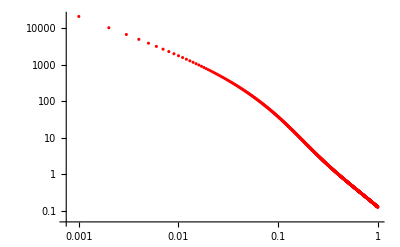

```mathematica
timePoints=Range[1,1000,1];

weightValues=Pnew/@timePoints;

(*Combine time points and their corresponding weights into a single list*)
Datatfix=Transpose[{timePoints,weightValues}];

sig=0.9;
f=sig/(2-sig);
N1= 1000/(1+f);
mu=10^-6;
L=10000;

theta=4 N1 mu L;
F=sig/(2-sig);
s=0.1;
h=0.5;
sa=s (h+ (1-h) F);
sb= s (1- (1-F) h);
x0=1/(2 2 sa N1);
x1=NDSolveValue[{D[x2a[t],t]==x2a[t]*(1-x2a[t]) (sa (1-x2a[t]) + sb x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[k,2]] G[x,Datatfix[[k,1]]]/(x*(1-x)),{k,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];

averageGData={};
AppendTo[averageGData,gData];


xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,gData};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red]
```

```mathematica
Quit[]
```

InterpolatingFunction::dmval: Input value {0.001,121752.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.002,60936.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.003,40665.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

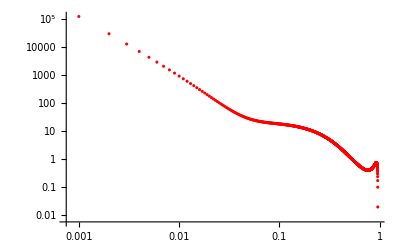

```mathematica
sig=0.9;
F=sig/(2-sig);
N1= 1000/(1+F);
mu=10^-6;
L=10000;

theta=4 N1 mu L;
F=sig/(2-sig);
s=0.1;
h=0.5;
sa=s (h+ (1-h) F);
sb= s (1- (1-F) h);
x0=1/(2 2 sa N1);
x1=NDSolveValue[{D[x2a[t],t]==x2a[t]*(1-x2a[t]) (sa (1-x2a[t]) + sb x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];
tfix=121.63;
G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[ G[x,tfix/(x*(1-x))],{x,0.001,0.999,0.001}];

averageGData={};
AppendTo[averageGData,gData];


xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,gData};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red]
```

```mathematica
timePoints=Range[1,1000,1];

weightValues=Pnew/@timePoints;

(*Combine time points and their corresponding weights into a single list*)
Datatfix=Transpose[{timePoints,weightValues}];

f=sig/(2-sig);
N1= 1000/(1+f);
mu=10^-6;
L=10000;

theta=4 N1 mu L;
F=sig/(2-sig);
s=0.1;
h=0.5;
sa=s (h+ (1-h) F);
sb= s (1- (1-F) h);
x0=1/(2 2 sa N1);
x1=NDSolveValue[{D[x2a[t],t]==x2a[t]*(1-x2a[t]) (sa (1-x2a[t]) + sb x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[k,2]] G[x,Datatfix[[k,1]]]/(x*(1-x)),{k,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];

averageGData={};
AppendTo[averageGData,gData];


xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis,gData};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Red]
```

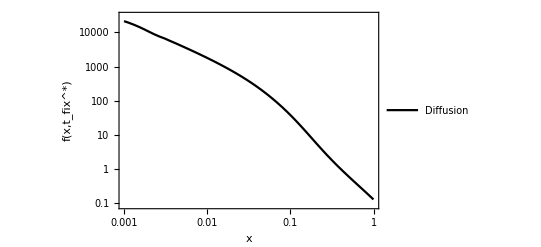

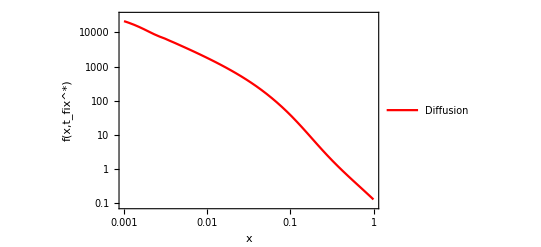

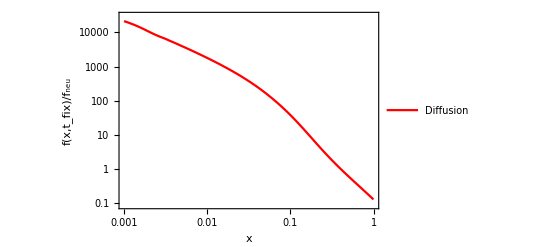

-Graphics-

```mathematica
(*Data1s=Transpose@{xaxis,gData};*)

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xMin_,xMax_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x is between xMin and xMax*)filteredData=Select[data,xMin<#[[1]]<xMax&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xMinThreshold=0.005;(*Lower threshold for binning*)xMaxThreshold=0.8;(*Upper threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xMinThreshold,xMaxThreshold];

(*Define a separate binning function for the upper part with 1000 bins*)
smoothUpperData[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>=xThreshold*)filteredData=Select[data,#[[1]]>=xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to the upper part of the data*)
numBinsUpper=20;(*Number of bins for the upper part*)upperSmoothedData=smoothUpperData[Data1s,numBinsUpper,xMaxThreshold];

(*Separate data into three parts:lower part (x<=xMinThreshold),middle part (xMinThreshold<x<xMaxThreshold),and upper part (x>=xMaxThreshold)*)
lowerPart=Select[Data1s,#[[1]]<=xMinThreshold&];
middlePart=Select[smoothedData,xMinThreshold<#[[1]]<xMaxThreshold&];
upperPart=Select[upperSmoothedData,#[[1]]>=xMaxThreshold&];

(*Combine all parts*)
combinedData=Join[lowerPart,middlePart,upperPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,\!\(\*SubscriptBox[\(t\), \(fix\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{" r = 10^-9 "},PlotRange->{{0.001,1},{0.1,10000}},PlotMarkers->{"●",10}];
(*a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"Diffusion"},PlotRange->{{0.001,1},{0.09,30000}}];*)

(*a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{Red},PlotLegends->{"Diffusion"},PlotRange->{{0.001,1},{0.09,30000}}];*)
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{Style["x",Italic,FontSize->16],Style["f(x,\!\(\*SubscriptBox[\(t\), \(fix\)]\))/\!\(\*SubscriptBox[\(f\), \(neu\)]\)",Italic,FontSize->16]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"Diffusion"},PlotRange->{{0.001,1},{0.09,30000}}];

a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[")  ",Italic](*,SubscriptBox[Style["f",Italic],"StyleBox[\"neu\",FontSlant->\"Italic\"]"]//DisplayForm,Style["(x)",Italic]*)}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium ,FontSize->16],PlotStyle->{Black},PlotLegends->{"Diffusion"},PlotRange->{{0.001,1},{0.09,30000}}];



(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
Transpose@{xaxis,gData}
```

```mathematica
Data1s={{0.001,21368.18911664683},{0.002,10477.734322126553},{0.003,6850.280772934423},{0.004,5038.543656319452},{0.005,3953.0663181203086},{0.006,3230.696796194738},{0.007,2715.798753761124},{0.008,2330.5542127288654},{0.009000000000000001,2031.7311314708504},{0.010000000000000002,1793.3904359283601},{0.011,1599.0255792006267},{0.012,1437.6323213361784},{0.013000000000000001,1301.592456909682},{0.014000000000000002,1185.4645164914896},{0.015,1085.258187526602},{0.016,997.9808273813984},{0.017,921.3440306067364},{0.018000000000000002,853.568007110957},{0.019000000000000003,793.2477356444733},{0.02,739.2592712368222},{0.021,690.6928219353522},{0.022000000000000002,646.804077340488},{0.023,606.9782340429222},{0.024,570.7030146996763},{0.025,537.5481625301323},{0.026000000000000002,507.14966784970034},{0.027000000000000003,479.19749981658936},{0.028,453.4259670883316},{0.029,429.6060728236723},{0.030000000000000002,407.5393986825407},{0.031,387.05317256646487},{0.032,367.99626115620066},{0.033,350.235891077452},{0.034,333.6549486830148},{0.035,318.1497427280426},{0.036000000000000004,303.6281399314306},{0.037000000000000005,290.0080028772927},{0.038,277.21587456228224},{0.039,265.18586531899143},{0.04,253.85870669960227},{0.041,243.18094381436765},{0.042,233.10424304912073},{0.043000000000000003,223.58479637915642},{0.044000000000000004,214.5828069118812},{0.045,206.06204302263882},{0.046,197.98945064560039},{0.047,190.33481505833376},{0.048,183.07046494219964},{0.049,176.17101267917778},{0.05,169.61312581200409},{0.051000000000000004,163.37532539029715},{0.052000000000000005,157.43780758340563},{0.053000000000000005,151.78228548699158},{0.054,146.3918485056502},{0.055,141.25083707459916},{0.056,136.3447308030513},{0.057,131.6600483909817},{0.058,127.1842578983633},{0.059000000000000004,122.905696138594},{0.060000000000000005,118.81349613163056},{0.061,114.89752169192651},{0.062,111.14830834563641},{0.063,107.557009873817},{0.064,104.11534986628223},{0.065,100.81557774649487},{0.066,97.65042879328308},{0.067,94.61308774180382},{0.068,91.6971555952867},{0.069,88.89661932182618},{0.07,86.20582414770846},{0.07100000000000001,83.61944819126967},{0.07200000000000001,81.13247920972644},{0.07300000000000001,78.74019325636387},{0.074,76.43813506735522},{0.075,74.22210001678556},{0.076,72.08811749542494},{0.077,70.03243558381536},{0.078,68.051506903513},{0.079,66.14197554207773},{0.08,64.30066495785819},{0.081,62.52456677988857},{0.082,60.810830426479924},{0.083,59.156753473453094},{0.084,57.559772709536794},{0.085,56.01745582233541},{0.08600000000000001,54.52749366353361},{0.08700000000000001,53.08769304672754},{0.08800000000000001,51.69597003550743},{0.089,50.35034368322724},{0.09,49.04893018932361},{0.091,47.78993744013601},{0.092,46.571659904966104},{0.093,45.392473860631895},{0.094,44.25083292004884},{0.095,43.1452638424292},{0.096,42.074362604558964},{0.097,41.036790714306825},{0.098,40.03127174905441},{0.099,39.05658810314111},{0.1,38.11157792968508},{0.101,37.19513226330191},{0.10200000000000001,36.3061923113027},{0.10300000000000001,35.44374690191352},{0.10400000000000001,34.606830078942174},{0.10500000000000001,33.794518833123696},{0.106,33.00593096111179},{0.107,32.240223043760224},{0.108,31.496588535956036},{0.109,30.774255960834886},{0.11,30.07248720173024},{0.111,29.39057588568696},{0.112,28.72784585280989},{0.113,28.08364970612591},{0.114,27.45736743700752},{0.115,26.848405121554585},{0.116,26.25619368364501},{0.117,25.680187720660246},{0.11800000000000001,25.119864388161513},{0.11900000000000001,24.574722340042733},{0.12000000000000001,24.04428072091906},{0.121,23.52807820772175},{0.122,23.025672097671126},{0.123,22.53663743998202},{0.124,22.06056620882617},{0.125,21.597066515236833},{0.126,21.153810222212666},{0.127,20.722244136486605},{0.128,20.301989474682063},{0.129,19.892681746020642},{0.13,19.49397017011705},{0.131,19.105517121217588},{0.132,18.726997597477474},{0.133,18.358098713957887},{0.134,17.998519218101844},{0.135,17.647969026520848},{0.136,17.306168781995012},{0.137,16.972849429650477},{0.138,16.647751811340644},{0.139,16.33062627731262},{0.14,16.02123231429175},{0.14100000000000001,15.719338189169106},{0.14200000000000002,15.424720607519163},{0.14300000000000002,15.13716438622129},{0.14400000000000002,14.856462139496537},{0.14500000000000002,14.58241397771116},{0.146,14.314827218332365},{0.147,14.053516108455957},{0.148,13.798301558356684},{0.149,13.549010885541733},{0.15,13.305477568815066},{0.151,13.067541011887032},{0.152,12.835046316087467},{0.153,12.607844061764219},{0.154,12.385790097970107},{0.155,12.168745340062559},{0.156,11.956575574858372},{0.157,11.749151273005479},{0.158,11.546347408249828},{0.159,11.348043283291599},{0.16,11.154122361941184},{0.161,10.964472107298656},{0.162,10.778983825694482},{0.163,10.597552516142848},{0.164,10.420076725069142},{0.165,10.246458406087202},{0.166,10.076602784610461},{0.167,9.911241244051105},{0.168,9.75108858901028},{0.169,9.594395461236134},{0.17,9.441069062989023},{0.171,9.291019493285008},{0.17200000000000001,9.144159654714755},{0.17300000000000001,9.000405163429155},{0.17400000000000002,8.859674262164372},{0.17500000000000002,8.721887736183605},{0.17600000000000002,8.586968832019117},{0.177,8.454843178903642},{0.178,8.325438712784155},{0.179,8.198685602817317},{0.18,8.074516180248546},{0.181,7.952864869582958},{0.182,7.833668121958591},{0.183,7.7168643506378585},{0.184,7.602393868535524},{0.185,7.490198827705719},{0.186,7.380223160713991},{0.187,7.2724125238228225},{0.188,7.166714241922719},{0.189,7.063077255143679},{0.19,6.9614520670845605},{0.191,6.8617906946001925},{0.192,6.764046619089262},{0.193,6.668174739227651},{0.194,6.574131325094596},{0.195,6.481873973640988},{0.196,6.391361565451438},{0.197,6.302554222753384},{0.198,6.215413268628565},{0.199,6.129901187384016},{0.2,6.045981586041409},{0.201,5.963619156905029},{0.202,5.882779641170601},{0.203,5.8034297935382355},{0.20400000000000001,5.725537347794629},{0.20500000000000002,5.649070983330592},{0.20600000000000002,5.574000292561647},{0.20700000000000002,5.500295749220449},{0.20800000000000002,5.427928677491019},{0.20900000000000002,5.357355966355163},{0.21,5.288301906564643},{0.211,5.22049389489407},{0.212,5.153903404362101},{0.213,5.08850267468998},{0.214,5.024264691677827},{0.215,4.961163167135692},{0.216,4.89917251935146},{0.217,4.838267854078039},{0.218,4.778424946022854},{0.219,4.719620220823631},{0.22,4.661830737494584},{0.221,4.605034171328035},{0.222,4.549208797236886},{0.223,4.4943334735240965},{0.224,4.440387626065092},{0.225,4.387351232890788},{0.226,4.335204809158146},{0.227,4.283929392496142},{0.228,4.233506528715673},{0.229,4.183918257871821},{0.23,4.135147100667775},{0.231,4.087176045189574},{0.232,4.039988533961868},{0.233,3.9935684513144656},{0.234,3.947900111050398},{0.23500000000000001,3.9029682444063263},{0.23600000000000002,3.8587579882962433},{0.23700000000000002,3.8152548738300576},{0.23800000000000002,3.7724448150987024},{0.23900000000000002,3.730314098217735},{0.24000000000000002,3.6888493706217216},{0.241,3.6480376306018742},{0.242,3.6078662170797253},{0.243,3.568322799609764},{0.244,3.529395368604345},{0.245,3.4910722257741647},{0.246,3.4533419747781218},{0.247,3.4161935120762625},{0.248,3.3796160179799086},{0.249,3.343598947893216},{0.25,3.3081320237405727},{0.251,3.2734293169716726},{0.252,3.2392548187853234},{0.253,3.20559806408461},{0.254,3.172448835798916},{0.255,3.1397971590913447},{0.256,3.1076332956944293},{0.257,3.0759477383705986},{0.258,3.0447312054938767},{0.259,3.0139746357495545},{0.26,2.9836691829485216},{0.261,2.953806210953155},{0.262,2.9243772887116593},{0.263,2.8953741853979604},{0.264,2.8667888656542377},{0.265,2.838613484933321},{0.266,2.810840384938268},{0.267,2.7834620891564166},{0.268,2.756471298485558},{0.269,2.729860886949514},{0.27,2.703623897500878},{0.271,2.677753537908619},{0.272,2.6522431767281214},{0.273,2.627086339351654},{0.274,2.6022767041370103},{0.275,2.5778080986122904},{0.276,2.5536744957548567},{0.277,2.529870010342397},{0.278,2.506388895374327},{0.279,2.4832255385616184},{0.28,2.460374458883221},{0.281,2.4378303032074164},{0.28200000000000003,2.4155878429764153},{0.28300000000000003,2.393641970952404},{0.28400000000000003,2.3719876980236347},{0.28500000000000003,2.350620150068876},{0.28600000000000003,2.3295345648787347},{0.28700000000000003,2.308726289132393},{0.28800000000000003,2.288190775428308},{0.28900000000000003,2.267923579367501},{0.29,2.2479203566880175},{0.291,2.2281768604493313},{0.292,2.208715832739623},{0.293,2.189559763146403},{0.294,2.1706504537018265},{0.295,2.1519836814399826},{0.296,2.1335553118114645},{0.297,2.11536129686047},{0.298,2.0973976734358466},{0.299,2.079660561435157},{0.3,2.0621461620809187},{0.301,2.044850756228412},{0.302,2.027770702704059},{0.303,2.0109024366738346},{0.304,1.994242468040944},{0.305,1.9777873798719205},{0.306,1.961533826850707},{0.307,1.945478533759854},{0.308,1.929618293988284},{0.309,1.9139499680649479},{0.31,1.8984704822177998},{0.311,1.8831768269574392},{0.312,1.868066055684882},{0.313,1.8531352833228476},{0.314,1.8383816849700478},{0.315,1.8238024945778788},{0.316,1.809395003649064},{0.317,1.795156559957654},{0.318,1.7810845662899157},{0.319,1.7671764792056373},{0.32,1.753429807819323},{0.321,1.7398421126008465},{0.322,1.7264110041950933},{0.323,1.7131341422601465},{0.324,1.7000092343235782},{0.325,1.687034034656407},{0.326,1.6742063431643683},{0.327,1.6615240042959898},{0.328,1.6489849059671717},{0.329,1.6365869785018339},{0.33,1.624328193588253},{0.331,1.6122065632507567},{0.332,1.60022013883636},{0.333,1.588367010016037},{0.334,1.57666518991683},{0.335,1.5651027415994165},{0.336,1.5536677767908846},{0.337,1.5423584032678945},{0.338,1.53117276384512},{0.339,1.5201090357300773},{0.34,1.5091654298881636},{0.341,1.4983401904176923},{0.342,1.4876315939347353},{0.343,1.4770379489675072},{0.34400000000000003,1.466557595360126},{0.34500000000000003,1.456188903685538},{0.34600000000000003,1.4459302746673968},{0.34700000000000003,1.4357801386107025},{0.34800000000000003,1.4257369548410468},{0.34900000000000003,1.4157992111522146},{0.35000000000000003,1.4059654232620369},{0.35100000000000003,1.3962341342762334},{0.35200000000000004,1.386603914160172},{0.353,1.377073359218257},{0.354,1.367641091580903},{0.355,1.3583057586988148},{0.356,1.3490660328445354},{0.357,1.3399206106209653},{0.358,1.3308682124768636},{0.359,1.3219075822290163},{0.36,1.3130374865910628},{0.361,1.3042567147087616},{0.362,1.2955640777015618},{0.363,1.2869584082103744},{0.364,1.2784385599513766},{0.365,1.2700034072757642},{0.366,1.2616518447352276},{0.367,1.2533827866531564},{0.368,1.2451951667013552},{0.369,1.2370879374821453},{0.37,1.2290600701158112},{0.371,1.2211105538332125},{0.372,1.2132383955734445},{0.373,1.2054426195864831},{0.374,1.1977222670406396},{0.375,1.190076395634801},{0.376,1.1825160945079154},{0.377,1.1750283608518977},{0.378,1.1676122485386558},{0.379,1.160266826910695},{0.38,1.1529911805280224},{0.381,1.1457844089185727},{0.382,1.138645626332091},{0.383,1.1315739614973401},{0.384,1.124568557382663},{0.385,1.1176285709597427},{0.386,1.1107531729705447},{0.387,1.1039415476973755},{0.388,1.097192892735981},{0.389,1.0905064187716345},{0.39,1.0838813493581407},{0.391,1.0773169206997386},{0.392,1.0708123814357733},{0.393,1.0643669924281587},{0.394,1.0579800265515142},{0.395,1.0516507684859757},{0.396,1.0453785145125694},{0.397,1.0391625723111466},{0.398,1.0330022607608011},{0.399,1.0268969097427318},{0.4,1.020845859945489},{0.401,1.01484846267256},{0.402,1.0089040796522635},{0.403,1.003012082849881},{0.404,0.9971718542820024},{0.405,0.9913827858329928},{0.406,0.9856442790736373},{0.40700000000000003,0.9799557450817875},{0.40800000000000003,0.9743166042650799},{0.40900000000000003,0.9687262861856261},{0.41000000000000003,0.9631842293866368},{0.41100000000000003,0.9576898812209731},{0.41200000000000003,0.9522426976815362},{0.41300000000000003,0.9468421432334968},{0.41400000000000003,0.941487690648309},{0.41500000000000004,0.9361788208394706},{0.41600000000000004,0.9309150226999942},{0.41700000000000004,0.9256973002915648},{0.418,0.9205266540165532},{0.419,0.9153995603472654},{0.42,0.9103155192605425},{0.421,0.9052740380778803},{0.422,0.9002746313552236},{0.423,0.895316820774065},{0.424,0.8904001350338501},{0.425,0.8855241097456583},{0.426,0.8806882873271226},{0.427,0.8758922168985986},{0.428,0.8711354541805021},{0.429,0.8664175613918627},{0.43,0.8617381071500103},{0.431,0.857096666371412},{0.432,0.8524928201736095},{0.433,0.8479261557782692},{0.434,0.8433962664152842},{0.435,0.8389027512279447},{0.436,0.8344452151791267},{0.437,0.8300232689585095},{0.438,0.8256365288907515},{0.439,0.8212846168446888},{0.44,0.8169671601434405},{0.441,0.812683791475476},{0.442,0.8084341488065869},{0.443,0.804217875292769},{0.444,0.8000346191939739},{0.445,0.7958840337887213},{0.446,0.7917657772895716},{0.447,0.7876795127594172},{0.448,0.7836249080285836},{0.449,0.7796016356127327},{0.45,0.7756093726315353},{0.451,0.7716478007281232},{0.452,0.767716605989265},{0.453,0.7638154788662983},{0.454,0.7599441140967536},{0.455,0.756102210626698},{0.456,0.752289471533752},{0.457,0.7485056039507885},{0.458,0.7447503189902708},{0.459,0.7410249578759515},{0.46,0.7373284181985311},{0.461,0.7336595985435003},{0.462,0.7300182148030672},{0.463,0.7264039865564215},{0.464,0.7228166370210274},{0.465,0.7192558930044417},{0.466,0.7157214848566505},{0.467,0.7122131464229112},{0.468,0.7087306149971054},{0.46900000000000003,0.7052736312755712},{0.47000000000000003,0.7018419393114272},{0.47100000000000003,0.6984352864693686},{0.47200000000000003,0.6950534233809268},{0.47300000000000003,0.6916961039001951},{0.47400000000000003,0.6883630850599942},{0.47500000000000003,0.6850541270284782},{0.47600000000000003,0.6817689930661935},{0.47700000000000004,0.6785074494835299},{0.47800000000000004,0.6752692655986267},{0.47900000000000004,0.672054213695657},{0.48000000000000004,0.668862068983537},{0.481,0.6656926095550165},{0.482,0.6625456163461628},{0.483,0.6594208730962321},{0.484,0.6563181663078955},{0.485,0.6532372852078498},{0.486,0.6501780217077802},{0.487,0.6471401703656773},{0.488,0.6441235283474915},{0.489,0.6411278953891402},{0.49,0.6381530737588368},{0.491,0.6351988682197472},{0.492,0.6322650859929665},{0.493,0.6293515367208198},{0.494,0.6264580324304443},{0.495,0.6235843874976881},{0.496,0.6207304186113091},{0.497,0.6178959447374468},{0.498,0.6150807870843806},{0.499,0.6122847690675749},{0.5,0.6095077162749748},{0.501,0.606750258443667},{0.502,0.604011419946471},{0.503,0.6012910292449717},{0.504,0.5985889168524662},{0.505,0.5959049153082643},{0.506,0.593238859152194},{0.507,0.5905905848993827},{0.508,0.5879599310152304},{0.509,0.585346737890639},{0.51,0.5827508478174491},{0.511,0.5801721049640995},{0.512,0.5776103553515007},{0.513,0.5750654468291246},{0.514,0.5725372290512933},{0.515,0.5700255534536712},{0.516,0.5675302732299703},{0.517,0.5650512433088266},{0.518,0.5625883203308917},{0.519,0.5601413626261051},{0.52,0.5577102301911357},{0.521,0.5552947846670334},{0.522,0.5528948893170276},{0.523,0.5505104090045254},{0.524,0.5481412101712595},{0.525,0.5457871608156137},{0.526,0.5434481304711168},{0.527,0.541123990185076},{0.528,0.5388146124973935},{0.529,0.5365198714195126},{0.53,0.5342396424135304},{0.531,0.5319738023714471},{0.532,0.5297222295945627},{0.533,0.5274848037730144},{0.534,0.5252614059654487},{0.535,0.5230519185788252},{0.536,0.5208562253483574},{0.537,0.5186742113175793},{0.538,0.5165057628185252},{0.539,0.5143507674520473},{0.54,0.512209114068244},{0.541,0.510080692746995},{0.542,0.5079656091699815},{0.543,0.5058639694745476},{0.544,0.5037752360151693},{0.545,0.5016993008404494},{0.546,0.4996360571438626},{0.547,0.4975853992511346},{0.548,0.4955472226077316},{0.549,0.49352142376646385},{0.55,0.4915079003751827},{0.551,0.4895065511645918},{0.552,0.4875172759361572},{0.553,0.4855399755501232},{0.554,0.4835745519136099},{0.555,0.48162090796883583},{0.556,0.47967894768141023},{0.557,0.4777485760287321},{0.558,0.4758296989884776},{0.559,0.4739222235271823},{0.56,0.472026057588903},{0.561,0.4701411100839755},{0.562,0.4682672908778548},{0.5630000000000001,0.4664045107800368},{0.5640000000000001,0.4645526815330642},{0.5650000000000001,0.4627117158016149},{0.5660000000000001,0.46088152716166386},{0.5670000000000001,0.459062030089732},{0.5680000000000001,0.4572531399521967},{0.5690000000000001,0.4554547729946913},{0.5700000000000001,0.45366684633156895},{0.5710000000000001,0.4518892779354408},{0.5720000000000001,0.45012198662678177},{0.5730000000000001,0.44836489206360436},{0.5740000000000001,0.44661791473120677},{0.5750000000000001,0.44488097593197357},{0.5760000000000001,0.44315399777524955},{0.5770000000000001,0.44143690316727485},{0.578,0.4397296158011765},{0.579,0.4380320601470251},{0.58,0.436344161441944},{0.581,0.4346658456802795},{0.582,0.43299703960382246},{0.583,0.43133767069208734},{0.584,0.4296878366731038},{0.585,0.4280473812952077},{0.586,0.42641614837805986},{0.587,0.42479406716409074},{0.588,0.4231810675891355},{0.589,0.4215770802754663},{0.59,0.41998203652487925},{0.591,0.4183958683118393},{0.592,0.4168185082766681},{0.593,0.41524988971880045},{0.594,0.413689946590073},{0.595,0.41213861348807934},{0.596,0.41059582564957114},{0.597,0.40906151894389453},{0.598,0.4075356298664998},{0.599,0.4060180955324703},{0.6,0.4045088536701227},{0.601,0.4030078426146296},{0.602,0.4015150013017064},{0.603,0.40003026926132934},{0.604,0.39855358661149826},{0.605,0.3970848940520474},{0.606,0.3956241328584868},{0.607,0.39417124487589683},{0.608,0.39272617251284786},{0.609,0.39128885873537267},{0.61,0.3898592470609632},{0.611,0.38843728155261475},{0.612,0.38702290681290247},{0.613,0.38561606797808967},{0.614,0.3842167107122746},{0.615,0.382824781201574},{0.616,0.38144022614832956},{0.617,0.38006299276535693},{0.618,0.3786930287702183},{0.619,0.37733028237953187},{0.62,0.3759747023033024},{0.621,0.3746262377392921},{0.622,0.37328483836740806},{0.623,0.37195045434412266},{0.624,0.37062303629692395},{0.625,0.3693025353187817},{0.626,0.3679889927264453},{0.627,0.36668227056952657},{0.628,0.36538232091840955},{0.629,0.3640890962871736},{0.63,0.362802549629045},{0.631,0.3615226343318762},{0.632,0.3602493042136526},{0.633,0.35898251351802135},{0.634,0.35772221690984923},{0.635,0.35646836947080357},{0.636,0.3552209266949505},{0.637,0.35397984448438674},{0.638,0.3527450791448829},{0.639,0.35151658738155916},{0.64,0.3502943262945741},{0.641,0.3490782533748362},{0.642,0.3478683264997346},{0.643,0.3466645039288972},{0.644,0.34546674429994534},{0.645,0.34427500662430127},{0.646,0.34308925028297693},{0.647,0.341909435022404},{0.648,0.3407355209502699},{0.649,0.3395674685313732},{0.65,0.33840523858349003},{0.651,0.3372487922732579},{0.652,0.3360980911120737},{0.653,0.33495309695200204},{0.654,0.333813771981696},{0.655,0.33268007872233557},{0.656,0.3315519800235689},{0.657,0.33042943905946753},{0.658,0.3293124193244962},{0.659,0.3282008846294809},{0.66,0.3270947990975974},{0.661,0.3259941271603598},{0.662,0.32489883355361726},{0.663,0.323808883313561},{0.664,0.32272424177273334},{0.665,0.3216448745560433},{0.666,0.3205707475767857},{0.667,0.31950189645408217},{0.668,0.31843835717326363},{0.669,0.31737995699283045},{0.67,0.3163266620427975},{0.671,0.315278438721001},{0.672,0.314235253691129},{0.673,0.31319707388077034},{0.674,0.3121638664794884},{0.675,0.31113559893690373},{0.676,0.3101122389608025},{0.677,0.3090937545152497},{0.678,0.30808011381873673},{0.679,0.3070712853423336},{0.68,0.3060672378078579},{0.681,0.30506794018606936},{0.682,0.3040733616948707},{0.683,0.3030834717975308},{0.684,0.30209824020092796},{0.685,0.3011176368537913},{0.686,0.3001416319449865},{0.687,0.2991701959017894},{0.6880000000000001,0.2982032993881921},{0.6890000000000001,0.2972409133032187},{0.6900000000000001,0.29628300877925906},{0.6910000000000001,0.2953295571804132},{0.6920000000000001,0.29438053010085635},{0.6930000000000001,0.2934358993632126},{0.6940000000000001,0.2924956370169483},{0.6950000000000001,0.29155971533678227},{0.6960000000000001,0.29062810682109985},{0.6970000000000001,0.28970078419039397},{0.6980000000000001,0.28877772038571153},{0.6990000000000001,0.2878588885671188},{0.7000000000000001,0.2869442621121776},{0.7010000000000001,0.2860338146144367},{0.7020000000000001,0.28512751988194285},{0.7030000000000001,0.2842253519357484},{0.7040000000000001,0.28332728500845417},{0.705,0.28243329354275154},{0.706,0.2815433521899811},{0.707,0.2806574358087043},{0.708,0.27977551946329127},{0.709,0.27889754167943953},{0.71,0.2780234962681814},{0.711,0.27715337747852936},{0.712,0.27628716142191795},{0.713,0.27542482440921934},{0.714,0.27456634294887927},{0.715,0.2737116937450577},{0.716,0.2728608536957763},{0.717,0.2720137998910725},{0.718,0.2711705096111548},{0.719,0.2703309603245663},{0.72,0.2694951296863509},{0.721,0.26866299553622225},{0.722,0.2678345358967399},{0.723,0.2670097289714843},{0.724,0.26618855314323725},{0.725,0.26537098697216915},{0.726,0.2645570091940162},{0.727,0.2637465987182751},{0.728,0.26293973462638764},{0.729,0.2621363961699318},{0.73,0.26133656276881356},{0.731,0.2605402140094565},{0.732,0.25974732964299235},{0.733,0.2589578895834577},{0.734,0.25817187390597907},{0.735,0.2573892628449666},{0.736,0.25661003679229627},{0.737,0.25583417629550126},{0.738,0.2550616620559576},{0.739,0.2542924749270575},{0.74,0.2535265959123964},{0.741,0.25276400616394096},{0.742,0.2520046869802013},{0.743,0.2512486198043972},{0.744,0.25049578622262075},{0.745,0.24974616796198496},{0.746,0.24899974688878054},{0.747,0.24825650500661367},{0.748,0.24751642445454206},{0.749,0.24677948750520312},{0.75,0.2460456765629342},{0.751,0.24531509978734112},{0.752,0.24458761434842877},{0.753,0.24386320249493285},{0.754,0.24314184659630633},{0.755,0.24242352914194984},{0.756,0.2417082327404478},{0.757,0.24099594011881273},{0.758,0.24028663412173504},{0.759,0.23958029771083852},{0.76,0.23887691396394575},{0.761,0.2381764660743469},{0.762,0.2374789373500776},{0.763,0.2367843112132009},{0.764,0.236092571199098},{0.765,0.23540370095576368},{0.766,0.23471768424311082},{0.767,0.23403450493227715},{0.768,0.23335414700494278},{0.769,0.23267659455265077},{0.77,0.23200183177613654},{0.771,0.2313298429846617},{0.772,0.23066061259535534},{0.773,0.22999412513256123},{0.774,0.2293303652271899},{0.775,0.22866931761608145},{0.776,0.22801096714136745},{0.777,0.22735529874984559},{0.778,0.2267022974923582},{0.779,0.22605194852317473},{0.78,0.22540423709938376},{0.781,0.22475914858028842},{0.782,0.22411666842681127},{0.783,0.22347678220090147},{0.784,0.22283947556495043},{0.785,0.22220473428121418},{0.786,0.22157254421123765},{0.787,0.22094289131529274},{0.788,0.22031576165181382},{0.789,0.2196911413768456},{0.79,0.21906901674349383},{0.791,0.21844937410138557},{0.792,0.21783219282852312},{0.793,0.2172174523316532},{0.794,0.21660515341885245},{0.795,0.21599528291163142},{0.796,0.21538782772622886},{0.797,0.21478277487291864},{0.798,0.21418011145531674},{0.799,0.21357982466969466},{0.8,0.21298190180429105},{0.801,0.21238633023862913},{0.802,0.21179309744283176},{0.803,0.21120219097693924},{0.804,0.21061359849023228},{0.805,0.21002730772055195},{0.806,0.20944330649362178},{0.807,0.20886158272237212},{0.808,0.20828212440626453},{0.809,0.2077049196306183},{0.81,0.2071299565659349},{0.811,0.2065572234672251},{0.812,0.2059867086733358},{0.8130000000000001,0.2054184006062762},{0.8140000000000001,0.20485228777054498},{0.8150000000000001,0.2042883587524564},{0.8160000000000001,0.20372660221946587},{0.8170000000000001,0.20316700691949602},{0.8180000000000001,0.20260956168025887},{0.8190000000000001,0.20205425540858069},{0.8200000000000001,0.2015010770897232},{0.8210000000000001,0.2009500157867036},{0.8220000000000001,0.20040106063961124},{0.8230000000000001,0.19985420086492742},{0.8240000000000001,0.19930942575483507},{0.8250000000000001,0.19876672467653225},{0.8260000000000001,0.1982260870715393},{0.8270000000000001,0.1976875024550051},{0.8280000000000001,0.19715096041500713},{0.8290000000000001,0.19661645061184915},{0.8300000000000001,0.19608396277735593},{0.8310000000000001,0.19555348671416117},{0.8320000000000001,0.19502501229499092},{0.8330000000000001,0.1944985294619441},{0.834,0.19397405919278965},{0.835,0.19345157632790386},{0.836,0.19293105540449026},{0.837,0.19241248643610348},{0.838,0.1918958594992841},{0.839,0.19138116473317768},{0.84,0.19086839233915284},{0.841,0.19035753258041918},{0.842,0.18984857578165323},{0.843,0.18934151232862048},{0.844,0.1888363326678028},{0.845,0.1883330273060311},{0.846,0.18783158681011358},{0.847,0.18733200180647022},{0.848,0.1868342629807703},{0.849,0.18633836107756815},{0.85,0.1858442868999452},{0.851,0.18535203130915112},{0.852,0.18486158522424653},{0.853,0.1843729396217519},{0.854,0.1838860855352919},{0.855,0.1834010140552471},{0.856,0.18291771632840523},{0.857,0.18243618355761326},{0.858,0.18195640700143187},{0.859,0.1814783779737935},{0.86,0.18100208784365937},{0.861,0.18052752803467736},{0.862,0.18005469002484584},{0.863,0.17958356534617329},{0.864,0.17911414558434338},{0.865,0.17864642237837985},{0.866,0.17818038742031195},{0.867,0.17771603245484094},{0.868,0.17725334927901062},{0.869,0.1767923297418763},{0.87,0.1763329657441716},{0.871,0.17587524923798412},{0.872,0.17541917222642406},{0.873,0.1749647267632998},{0.874,0.1745119049527856},{0.875,0.1740606989491018},{0.876,0.1736111098624427},{0.877,0.17316312112546858},{0.878,0.17271672500394677},{0.879,0.172271913811533},{0.88,0.17182867990949902},{0.881,0.17138701570646112},{0.882,0.1709469136581133},{0.883,0.17050836626695898},{0.884,0.17007136608204823},{0.885,0.16963590569871181},{0.886,0.16920197775830462},{0.887,0.1687695749479417},{0.888,0.16833869000024287},{0.889,0.16790931569307624},{0.89,0.16748144484930463},{0.891,0.16705507033653172},{0.892,0.16663018506685343},{0.893,0.1662067819966056},{0.894,0.16578485412612037},{0.895,0.16536439449947699},{0.896,0.1649453962042601},{0.897,0.16452785237131612},{0.898,0.16411175617451176},{0.899,0.16369710083049704},{0.9,0.1632838795984644},{0.901,0.16287208577991558},{0.902,0.16246171271842544},{0.903,0.1620527537994091},{0.904,0.16164520244989133},{0.905,0.16123905213827586},{0.906,0.16083429637411695},{0.907,0.16043092870789388},{0.908,0.16002894273078322},{0.909,0.15962833207443777},{0.91,0.15922909041076136},{0.911,0.15883121145169113},{0.912,0.15843468894897458},{0.913,0.15803951669395308},{0.914,0.15764568851734737},{0.915,0.15725319828903825},{0.916,0.15686203991785624},{0.917,0.15647220735136805},{0.918,0.15608369457566382},{0.919,0.1556964956151517},{0.92,0.15531060453234494},{0.921,0.15492601542765863},{0.922,0.15454272243920142},{0.923,0.15416071974257411},{0.924,0.15378000155066412},{0.925,0.15340056211344585},{0.926,0.15302239571777862},{0.927,0.15264549668721006},{0.928,0.15226985938177645},{0.929,0.15189547819780685},{0.93,0.15152234756772928},{0.931,0.1511504619598738},{0.932,0.15077981587828349},{0.933,0.1504104038625213},{0.934,0.15004222048747917},{0.935,0.1496752603631901},{0.936,0.14930951813464105},{0.937,0.14894498848158488},{0.9380000000000001,0.14858166611835605},{0.9390000000000001,0.1482195457936861},{0.9400000000000001,0.14785862229052127},{0.9410000000000001,0.14749889042584},{0.9420000000000001,0.147140345050472},{0.9430000000000001,0.14678298104891974},{0.9440000000000001,0.14642679333917963},{0.9450000000000001,0.14607177687256578},{0.9460000000000001,0.14571792663353086},{0.9470000000000001,0.14536523763949477},{0.9480000000000001,0.14501370494066906},{0.9490000000000001,0.14466332361988374},{0.9500000000000001,0.14431408879241653},{0.9510000000000001,0.1439659956058222},{0.9520000000000001,0.14361903923976208},{0.9530000000000001,0.14327321490583725},{0.9540000000000001,0.14292851784741947},{0.9550000000000001,0.1425849433394855},{0.9560000000000001,0.1422424866884516},{0.9570000000000001,0.14190114323201083},{0.9580000000000001,0.14156090833896737},{0.9590000000000001,0.1412217774090752},{0.9600000000000001,0.14088374587287866},{0.961,0.14054680919154908},{0.962,0.14021096285672824},{0.963,0.13987620239036797},{0.964,0.13954252334457687},{0.965,0.139209921301458},{0.966,0.13887839187295903},{0.967,0.13854793070071578},{0.968,0.13821853345589719},{0.969,0.13789019583905684},{0.97,0.13756291357997943},{0.971,0.137236682437528},{0.972,0.13691149819949805},{0.973,0.1365873566824673},{0.974,0.13626425373164766},{0.975,0.13594218522073842},{0.976,0.13562114705178097},{0.977,0.13530113515501394},{0.978,0.13498214548872742},{0.979,0.13466417403912107},{0.98,0.1343472168201615},{0.981,0.1340312698734412},{0.982,0.1337163292680363},{0.983,0.1334023911003687},{0.984,0.13308945149406515},{0.985,0.13277750659982146},{0.986,0.13246655259526283},{0.987,0.13215658568480973},{0.988,0.1318476020995408},{0.989,0.13153959809705762},{0.99,0.13123256996135263},{0.991,0.13092651400267477},{0.992,0.13062142655739623},{0.993,0.13031730398788344},{0.994,0.13001414268236386},{0.995,0.12971193905479736},{0.996,0.12941068954474674},{0.997,0.1291103906172494},{0.998,0.1288110387626893},{0.999,0.1285126304966704}};
```